## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=10 TeV, C_ν_Ri^Z'≈ 0.1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime10=10;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
e^2/(sinsquared(1-sinsquared))
```

0.515835

```mathematica
Zprime10decaymassless01=MassZprime10/(12π)((gVZp01)^2+(gAZp01)^2)*10^3
```

2.64916

```mathematica
Zprime10decaymassless01plot=MassZprime10/(12π)((GVZp01)^2+(GAZp01)^2)*10^3;
```

```mathematica
Plot3D[Zprime10decaymassless01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ(GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=8 TeV, C_ν_Ri^Z'≈ 0.1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime8=8;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
Zprime8decaymassless01=MassZprime8/(12π)((gVZp01)^2+(gAZp01)^2)*10^3
```

2.11933

```mathematica
Zprime8decaymassless01plot=MassZprime8/(12π)((GVZp01)^2+(GAZp01)^2)*10^3;
```

```mathematica
Plot3D[Zprime8decaymassless01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ(GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=5 TeV, C_ν_Ri^Z'≈ 0.1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime5=5;
```

```mathematica
gVZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.1))
gAZp01=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.0999355

-0.0000644793

```mathematica
Zprime5decaymassless01=MassZprime5/(12π)((gVZp01)^2+(gAZp01)^2)*10^3
```

1.32458

```mathematica
Zprime5decaymassless01plot=MassZprime5/(12π)((GVZp01)^2+(GAZp01)^2)*10^3;
```

```mathematica
Plot3D[Zprime5decaymassless01plot,{GVZp01,0,1},{GAZp01,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ(GeV)"}]
```

-Graphics3D-

## Compare Change in Z-Prime mass

```mathematica
Zprime10decaymassless01
Zprime8decaymassless01
Zprime5decaymassless01
```

2.64916

2.11933

1.32458

```mathematica
Zprimedecay01[Mz_]:=Mz/(12π)((gVZp01)^2+(gAZp01)^2)*10^3
```

```mathematica
Zprimedecay01[5]
Zprimedecay01[6]
Zprimedecay01[7]
Zprimedecay01[8]
Zprimedecay01[9]
Zprimedecay01[10]
Zprimedecay01[11]
Zprimedecay01[12]
```

1.32458

1.5895

1.85441

2.11933

2.38425

2.64916

2.91408

3.179

```mathematica
DecayTable01=TableForm[{{5,Zprimedecay01[5]},{6,Zprimedecay01[6]},{7,Zprimedecay01[7]},{8,Zprimedecay01[8]},{9,Zprimedecay01[9]},{10,Zprimedecay01[10]},{11,Zprimedecay01[11]},{12,Zprimedecay01[12]}},TableHeadings-> {None,{"TeV","Decay Rate(GeV)"}}]
```

TeV | Decay Rate(GeV)
5 | 1.32458
6 | 1.5895
7 | 1.85441
8 | 2.11933
9 | 2.38425
10 | 2.64916
11 | 2.91408
12 | 3.179

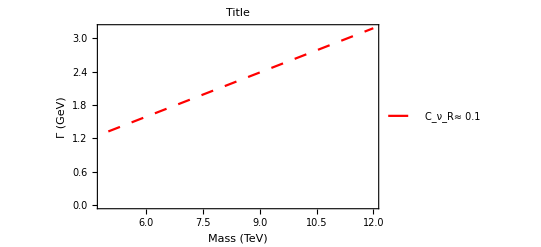

```mathematica
PlotZprimeDecay01=ListPlot[%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{" C_ν_R≈ 0.1"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## *Note each end result is multiplied by 10^3to bring Decay Rate units in MeV